## Get helper functions

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]]
```

## Testing

```mathematica
data = readBeamFile["~/BC14_chirp+0_0.h5_streaked.h5"];
data = RandomSample[data,100000];

densityHistogramMod[10^3{#x,#y}&/@data,{100,100},LabelStyle->20,ImageSize->400,AspectRatio->Automatic]
```

-Graphics-

```mathematica
step = 0.01;
xMin = -0.5;
xMax = 1.2;
yMin = -1;
yMax = 1;
binData = BinCounts[ 
10^3{#x,#y}&/@data,
{xMin,xMax,step},
{yMin,yMax,step}
];
binData = GaussianFilter[binData,3];

binXYData = Table[
{
xMin + step*xII,
yMin+ step*yII,
binData[[xII,yII]]
},

{yII,Length[binData[[1]]]},
{xII,Length[binData]}


];
binXYData = Flatten[binXYData,1];
```

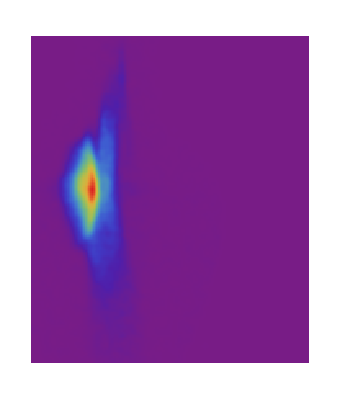

```mathematica
ArrayPlot[Reverse[Transpose[binData]],ColorFunction->"Rainbow"]
```

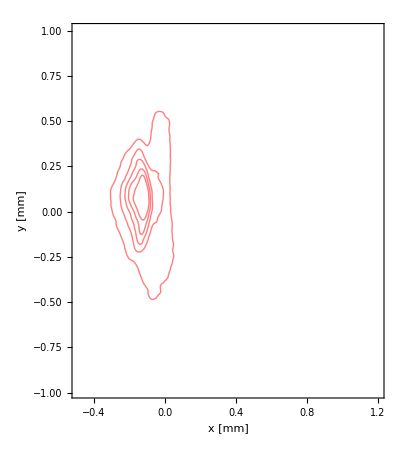

```mathematica
ListContourPlot[
binXYData,
ColorFunction->"Rainbow",
ContourShading->None,
ContourStyle->Red,
PlotRange->All,
ImageSize->400,
Frame->True,
FrameLabel->{"x [mm]","y [mm]"},
LabelStyle->20,
AspectRatio->Automatic,
Contours->{10,30,50,70,90}
]
```

## Create figures

This is just a gross copy/paste of above

### 2D 0_0

```mathematica
data = readBeamFile["~/chirp0_0.2Dcsr.json_streaked.h5"];
data = RandomSample[data,100000];

densityHistogramMod[10^3{#x,#y}&/@data,{100,100},LabelStyle->20,ImageSize->400,AspectRatio->Automatic]
```

-Graphics-

```mathematica
step = 0.01;
xMin = -0.5;
xMax = 1.2;
yMin = -1;
yMax = 1;
binData = BinCounts[ 
10^3{#x,#y}&/@data,
{xMin,xMax,step},
{yMin,yMax,step}
];
binData = GaussianFilter[binData,3];

binXYData = Table[
{
xMin + step*xII,
yMin+ step*yII,
binData[[xII,yII]]
},

{yII,Length[binData[[1]]]},
{xII,Length[binData]}


];
binXYData = Flatten[binXYData,1];
```

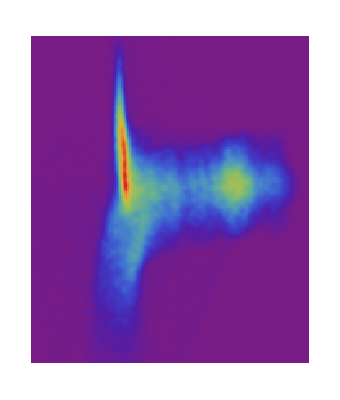

```mathematica
ArrayPlot[Reverse[Transpose[binData]],ColorFunction->"Rainbow"]
```

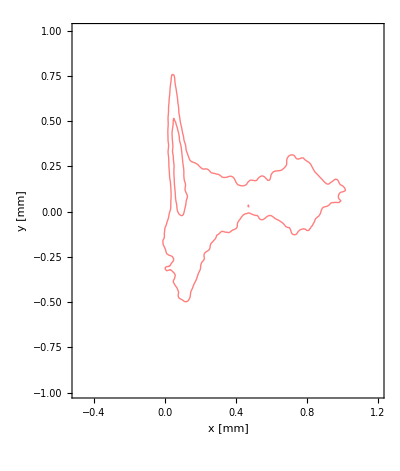

```mathematica
ListContourPlot[
binXYData,
ColorFunction->"Rainbow",
ContourShading->None,
ContourStyle->Red,
PlotRange->All,
ImageSize->400,
Frame->True,
FrameLabel->{"x [mm]","y [mm]"},
LabelStyle->20,
AspectRatio->Automatic,
Contours->{10,30,50,70,90}
]
```

```mathematica
binXYData2D00 = binXYData;
```

### 1D 0_0

```mathematica
data = readBeamFile["~/chirp0_0.1Dcsr.json_streaked.h5"];
data = RandomSample[data,100000];

densityHistogramMod[10^3{#x,#y}&/@data,{100,100},LabelStyle->20,ImageSize->400,AspectRatio->Automatic]
```

-Graphics-

```mathematica
step = 0.01;
xMin = -0.5;
xMax = 1.2;
yMin = -1;
yMax = 1;
binData = BinCounts[ 
10^3{#x,#y}&/@data,
{xMin,xMax,step},
{yMin,yMax,step}
];
binData = GaussianFilter[binData,3];

binXYData = Table[
{
xMin + step*xII,
yMin+ step*yII,
binData[[xII,yII]]
},

{yII,Length[binData[[1]]]},
{xII,Length[binData]}


];
binXYData = Flatten[binXYData,1];
```

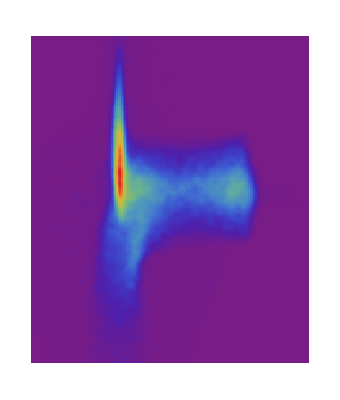

```mathematica
ArrayPlot[Reverse[Transpose[binData]],ColorFunction->"Rainbow"]
```

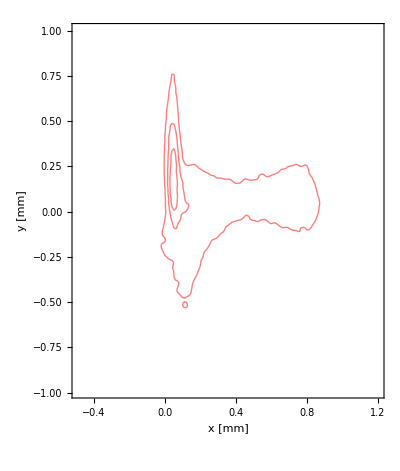

```mathematica
ListContourPlot[
binXYData,
ColorFunction->"Rainbow",
ContourShading->None,
ContourStyle->Red,
PlotRange->All,
ImageSize->400,
Frame->True,
FrameLabel->{"x [mm]","y [mm]"},
LabelStyle->20,
AspectRatio->Automatic,
Contours->{10,30,50,70,90}
]
```

```mathematica
binXYData1D00 = binXYData;
```

### Combined

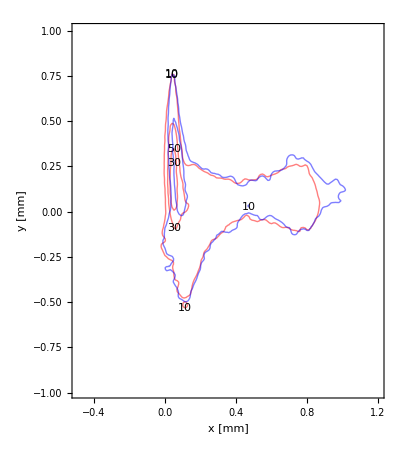

```mathematica
Show[
ListContourPlot[
binXYData1D00,
ColorFunction->"Rainbow",
ContourShading->None,
ContourStyle->Red,
PlotRange->All,
ImageSize->400,
Frame->True,
FrameLabel->{"x [mm]","y [mm]"},
LabelStyle->20,
AspectRatio->Automatic,
Contours->{10,30,50,70,90},
ContourLabels->All
],
ListContourPlot[
binXYData2D00,
ColorFunction->"Rainbow",
ContourShading->None,
ContourStyle->Blue,
PlotRange->All,
ImageSize->400,
Frame->True,
FrameLabel->{"x [mm]","y [mm]"},
LabelStyle->20,
AspectRatio->Automatic,
Contours->{10,30,50,70,90},
ContourLabels->All
]


]
```

### 2D 0_05

```mathematica
data = readBeamFile["~/chirp0_05.2Dcsr.json_streaked.h5"];
data = RandomSample[data,100000];

densityHistogramMod[10^3{#x,#y}&/@data,{100,100},LabelStyle->20,ImageSize->400,AspectRatio->Automatic]
```

-Graphics-

```mathematica
step = 0.01;
xMin = -0.5;
xMax = 1.2;
yMin = -1;
yMax = 1;
binData = BinCounts[ 
10^3{#x,#y}&/@data,
{xMin,xMax,step},
{yMin,yMax,step}
];
binData = GaussianFilter[binData,3];

binXYData = Table[
{
xMin + step*xII,
yMin+ step*yII,
binData[[xII,yII]]
},

{yII,Length[binData[[1]]]},
{xII,Length[binData]}


];
binXYData = Flatten[binXYData,1];
```

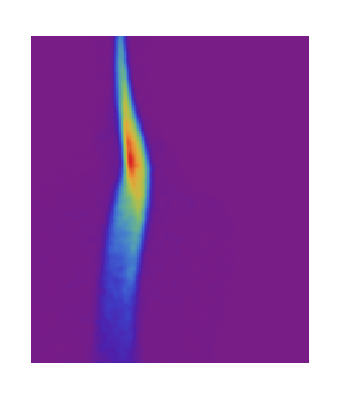

```mathematica
ArrayPlot[Reverse[Transpose[binData]],ColorFunction->"Rainbow"]
```

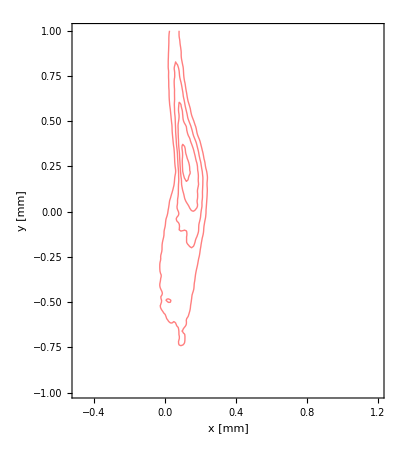

```mathematica
ListContourPlot[
binXYData,
ColorFunction->"Rainbow",
ContourShading->None,
ContourStyle->Red,
PlotRange->All,
ImageSize->400,
Frame->True,
FrameLabel->{"x [mm]","y [mm]"},
LabelStyle->20,
AspectRatio->Automatic,
Contours->{10,30,50,70,90}
]
```

```mathematica
binXYData2D05 = binXYData;
```

### 1D 0_05

```mathematica
data = readBeamFile["~/chirp0_05.1Dcsr.json_streaked.h5"];
data = RandomSample[data,100000];

densityHistogramMod[10^3{#x,#y}&/@data,{100,100},LabelStyle->20,ImageSize->400,AspectRatio->Automatic]
```

-Graphics-

```mathematica
step = 0.01;
xMin = -0.5;
xMax = 1.2;
yMin = -1;
yMax = 1;
binData = BinCounts[ 
10^3{#x,#y}&/@data,
{xMin,xMax,step},
{yMin,yMax,step}
];
binData = GaussianFilter[binData,3];

binXYData = Table[
{
xMin + step*xII,
yMin+ step*yII,
binData[[xII,yII]]
},

{yII,Length[binData[[1]]]},
{xII,Length[binData]}


];
binXYData = Flatten[binXYData,1];
```

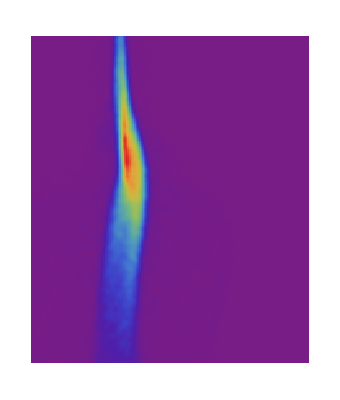

```mathematica
ArrayPlot[Reverse[Transpose[binData]],ColorFunction->"Rainbow"]
```

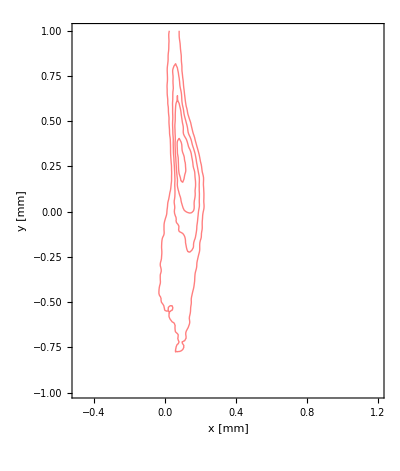

```mathematica
ListContourPlot[
binXYData,
ColorFunction->"Rainbow",
ContourShading->None,
ContourStyle->Red,
PlotRange->All,
ImageSize->400,
Frame->True,
FrameLabel->{"x [mm]","y [mm]"},
LabelStyle->20,
AspectRatio->Automatic,
Contours->{10,30,50,70,90}
]
```

```mathematica
binXYData1D05 = binXYData;
```

### Combined

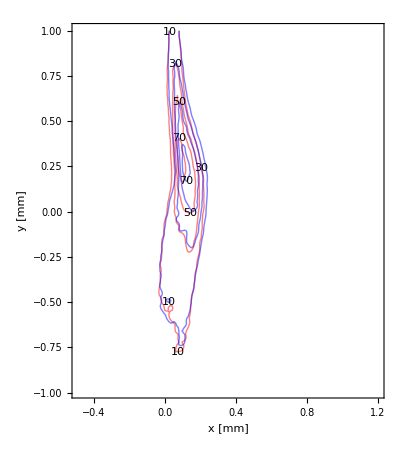

```mathematica
Show[
ListContourPlot[
binXYData1D05,
ColorFunction->"Rainbow",
ContourShading->None,
ContourStyle->Red,
PlotRange->All,
ImageSize->400,
Frame->True,
FrameLabel->{"x [mm]","y [mm]"},
LabelStyle->20,
AspectRatio->Automatic,
Contours->{10,30,50,70,90},
ContourLabels->All
],
ListContourPlot[
binXYData2D05,
ColorFunction->"Rainbow",
ContourShading->None,
ContourStyle->Blue,
PlotRange->All,
ImageSize->400,
Frame->True,
FrameLabel->{"x [mm]","y [mm]"},
LabelStyle->20,
AspectRatio->Automatic,
Contours->{10,30,50,70,90},
ContourLabels->All
]


]
```